```mathematica
$Assumptions=And[q1>0,q2>0,dq>0,t1>0,t2>0,x>0];
```

```mathematica
eq1=(1-q1*t1)(1-q2*t2)*ⅇ^(-q1*t1-q2*t2)-(1-q1*t2)(1-q2*t1)*ⅇ^(-q1*t2-q2*t1);
```

```mathematica
q2dq={q2->q1+dq};
```

```mathematica
q1dq=Solve[(eq1/.q2dq)==0,q1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q1→1/(2 (ⅇ^(dq t1)-ⅇ^(dq t2)) t1 t2)(ⅇ^(dq t1) t1-ⅇ^(dq t2) t1+ⅇ^(dq t1) t2-ⅇ^(dq t2) t2-dq ⅇ^(dq t1) t1 t2+dq ⅇ^(dq t2) t1 t2-√(-4 (ⅇ^(dq t1)-ⅇ^(dq t2)) t1 t2 (ⅇ^(dq t1)-ⅇ^(dq t2)+dq ⅇ^(dq t2) t1-dq ⅇ^(dq t1) t2)+(-ⅇ^(dq t1) t1+ⅇ^(dq t2) t1-ⅇ^(dq t1) t2+ⅇ^(dq t2) t2+dq ⅇ^(dq t1) t1 t2-dq ⅇ^(dq t2) t1 t2)^2))},{q1→1/(2 (ⅇ^(dq t1)-ⅇ^(dq t2)) t1 t2)(ⅇ^(dq t1) t1-ⅇ^(dq t2) t1+ⅇ^(dq t1) t2-ⅇ^(dq t2) t2-dq ⅇ^(dq t1) t1 t2+dq ⅇ^(dq t2) t1 t2+√(-4 (ⅇ^(dq t1)-ⅇ^(dq t2)) t1 t2 (ⅇ^(dq t1)-ⅇ^(dq t2)+dq ⅇ^(dq t2) t1-dq ⅇ^(dq t1) t2)+(-ⅇ^(dq t1) t1+ⅇ^(dq t2) t1-ⅇ^(dq t1) t2+ⅇ^(dq t2) t2+dq ⅇ^(dq t1) t1 t2-dq ⅇ^(dq t2) t1 t2)^2))}}

```mathematica
Simplify[q1/.(q1dq[[1]])]
```

-(-ⅇ^(dq t1) t1+ⅇ^(dq t2) t1-ⅇ^(dq t1) t2+ⅇ^(dq t2) t2+dq ⅇ^(dq t1) t1 t2-dq ⅇ^(dq t2) t1 t2+√((ⅇ^(dq t1)-ⅇ^(dq t2)) ((ⅇ^(dq t1)-ⅇ^(dq t2)) (t1+t2-dq t1 t2)^2+4 t1 t2 (ⅇ^(dq t2) (1-dq t1)+ⅇ^(dq t1) (-1+dq t2)))))/(2 (ⅇ^(dq t1)-ⅇ^(dq t2)) t1 t2)

```mathematica
rad=((ⅇ^(dq t1)-ⅇ^(dq t2)) ((ⅇ^(dq t1)-ⅇ^(dq t2)) (t1+t2-dq t1 t2)^2+4 t1 t2 (ⅇ^(dq t2) (1-dq t1)+ⅇ^(dq t1) (-1+dq t2))));
```

```mathematica
Simplify[Expand[rad]]
```

ⅇ^(2 dq t2) (t1-t2+dq t1 t2)^2+ⅇ^(2 dq t1) (t2+t1 (-1+dq t2))^2-2 ⅇ^(dq (t1+t2)) (-2 t1 t2+t2^2+t1^2 (1+dq^2 t2^2))

```mathematica
qq1p=1/(2*t1*t2(ⅇ^(-dq*t1)-ⅇ^(-dq*t2)))((ⅇ^(-dq*t1)-ⅇ^(-dq*t2))(t1+t2-dq*t1*t2)+√(((t1-t2)^2+(dq*t1*t2)^2)(ⅇ^(-dq*t1)-ⅇ^(-dq*t2))^2+2(t1-t2)(dq*t1*t2)(ⅇ^(-2*dq*t1)-ⅇ^(-2*dq*t2))));
```

```mathematica
qq1m=1/(2*t1*t2(ⅇ^(-dq*t1)-ⅇ^(-dq*t2)))((ⅇ^(-dq*t1)-ⅇ^(-dq*t2))(t1+t2-dq*t1*t2)-√(((t1-t2)^2+(dq*t1*t2)^2)(ⅇ^(-dq*t1)-ⅇ^(-dq*t2))^2+2(t1-t2)(dq*t1*t2)(ⅇ^(-2*dq*t1)-ⅇ^(-2*dq*t2))));
```

```mathematica
Simplify[(q1/.(q1dq[[1]]))-qq1p]
```

0

```mathematica
Simplify[(q1/.(q1dq[[2]]))-qq1m]
```

0

```mathematica
eq2=(1-q2*t2)*q1^2*ⅇ^(-q1*t1)-(1-q1*t2)*q2^2*ⅇ^(-q2*t1);
```

```mathematica
eq2q2=FullSimplify[eq2/ⅇ^(-q1*t1)/.q2dq]
```

ⅇ^(-dq t1) (dq+q1)^2 (-1+q1 t2)+q1^2 (1-(dq+q1) t2)

```mathematica
eq2dqp=Simplify[Expand[eq2q2/.(q1->qq1p)]]
```

1/(2 (ⅇ^(dq t1)-ⅇ^(dq t2))^2 t1^3 t2)ⅇ^(-dq t1) (-dq ⅇ^(2 dq t1) t1^3+dq ⅇ^(dq (t1+t2)) t1^3+dq ⅇ^(dq (2 t1+t2)) t1^3-dq ⅇ^(dq (t1+2 t2)) t1^3-ⅇ^(2 dq t1) t1 t2+ⅇ^(3 dq t1) t1 t2-ⅇ^(2 dq t2) t1 t2+2 ⅇ^(dq (t1+t2)) t1 t2-2 ⅇ^(dq (2 t1+t2)) t1 t2+ⅇ^(dq (t1+2 t2)) t1 t2-2 dq ⅇ^(2 dq t1) t1^2 t2+2 dq ⅇ^(dq (t1+t2)) t1^2 t2+2 dq ⅇ^(dq (2 t1+t2)) t1^2 t2-2 dq ⅇ^(dq (t1+2 t2)) t1^2 t2-dq^2 ⅇ^(2 dq t1) t1^3 t2+dq^2 ⅇ^(dq (t1+t2)) t1^3 t2-dq^2 ⅇ^(dq (2 t1+t2)) t1^3 t2+dq^2 ⅇ^(dq (t1+2 t2)) t1^3 t2+ⅇ^(2 dq t1) t2^2-ⅇ^(3 dq t1) t2^2+ⅇ^(2 dq t2) t2^2-2 ⅇ^(dq (t1+t2)) t2^2+2 ⅇ^(dq (2 t1+t2)) t2^2-ⅇ^(dq (t1+2 t2)) t2^2+2 dq ⅇ^(2 dq t1) t1 t2^2-dq ⅇ^(3 dq t1) t1 t2^2-dq ⅇ^(2 dq t2) t1 t2^2-dq ⅇ^(dq (t1+t2)) t1 t2^2-dq ⅇ^(dq (2 t1+t2)) t1 t2^2+2 dq ⅇ^(dq (t1+2 t2)) t1 t2^2+dq^2 ⅇ^(2 dq t1) t1^2 t2^2-dq^2 ⅇ^(dq (t1+t2)) t1^2 t2^2+dq^2 ⅇ^(dq (2 t1+t2)) t1^2 t2^2-dq^2 ⅇ^(dq (t1+2 t2)) t1^2 t2^2-dq ⅇ^(2 dq (t1+t2)) t1^2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+dq ⅇ^(dq (2 t1+t2)) t1^2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-ⅇ^(2 dq (t1+t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-ⅇ^(dq (2 t1+t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+ⅇ^(dq (3 t1+t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+ⅇ^(dq (t1+2 t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+dq ⅇ^(2 dq (t1+t2)) t1 t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-dq ⅇ^(dq (2 t1+t2)) t1 t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2)))

```mathematica
eq2dqm=Simplify[Expand[eq2q2/.(q1->qq1m)]]
```

1/(2 (ⅇ^(dq t1)-ⅇ^(dq t2))^2 t1^3 t2)ⅇ^(-dq t1) (-dq ⅇ^(2 dq t1) t1^3+dq ⅇ^(dq (t1+t2)) t1^3+dq ⅇ^(dq (2 t1+t2)) t1^3-dq ⅇ^(dq (t1+2 t2)) t1^3-ⅇ^(2 dq t1) t1 t2+ⅇ^(3 dq t1) t1 t2-ⅇ^(2 dq t2) t1 t2+2 ⅇ^(dq (t1+t2)) t1 t2-2 ⅇ^(dq (2 t1+t2)) t1 t2+ⅇ^(dq (t1+2 t2)) t1 t2-2 dq ⅇ^(2 dq t1) t1^2 t2+2 dq ⅇ^(dq (t1+t2)) t1^2 t2+2 dq ⅇ^(dq (2 t1+t2)) t1^2 t2-2 dq ⅇ^(dq (t1+2 t2)) t1^2 t2-dq^2 ⅇ^(2 dq t1) t1^3 t2+dq^2 ⅇ^(dq (t1+t2)) t1^3 t2-dq^2 ⅇ^(dq (2 t1+t2)) t1^3 t2+dq^2 ⅇ^(dq (t1+2 t2)) t1^3 t2+ⅇ^(2 dq t1) t2^2-ⅇ^(3 dq t1) t2^2+ⅇ^(2 dq t2) t2^2-2 ⅇ^(dq (t1+t2)) t2^2+2 ⅇ^(dq (2 t1+t2)) t2^2-ⅇ^(dq (t1+2 t2)) t2^2+2 dq ⅇ^(2 dq t1) t1 t2^2-dq ⅇ^(3 dq t1) t1 t2^2-dq ⅇ^(2 dq t2) t1 t2^2-dq ⅇ^(dq (t1+t2)) t1 t2^2-dq ⅇ^(dq (2 t1+t2)) t1 t2^2+2 dq ⅇ^(dq (t1+2 t2)) t1 t2^2+dq^2 ⅇ^(2 dq t1) t1^2 t2^2-dq^2 ⅇ^(dq (t1+t2)) t1^2 t2^2+dq^2 ⅇ^(dq (2 t1+t2)) t1^2 t2^2-dq^2 ⅇ^(dq (t1+2 t2)) t1^2 t2^2+dq ⅇ^(2 dq (t1+t2)) t1^2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-dq ⅇ^(dq (2 t1+t2)) t1^2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+ⅇ^(2 dq (t1+t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+ⅇ^(dq (2 t1+t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-ⅇ^(dq (3 t1+t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-ⅇ^(dq (t1+2 t2)) t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))-dq ⅇ^(2 dq (t1+t2)) t1 t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2))+dq ⅇ^(dq (2 t1+t2)) t1 t2 √(2 dq (ⅇ^(-2 dq t1)-ⅇ^(-2 dq t2)) t1 (t1-t2) t2+(ⅇ^(-dq t1)-ⅇ^(-dq t2))^2 ((t1-t2)^2+dq^2 t1^2 t2^2)))

```mathematica
tvals={t1->2,t2->25};
```

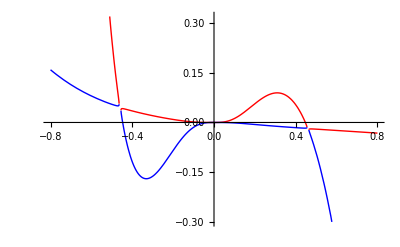

```mathematica
Plot[{eq2dqp/.tvals,eq2dqm/.tvals},{dq,-0.8,0.8},PlotStyle->{Red,Blue}]
```

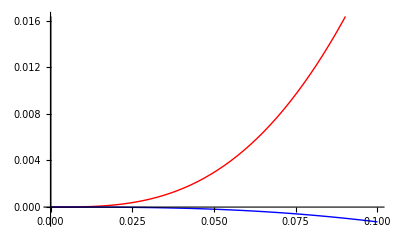

```mathematica
Plot[{eq2dqp/.tvals,eq2dqm/.tvals},{dq,0,0.1},PlotStyle->{Red,Blue}]
```

```mathematica
radd=Simplify[(((t1-t2)^2+(dq*t1*t2)^2)(ⅇ^(-dq*t1)-ⅇ^(-dq*t2))^2+2(t1-t2)(dq*t1*t2)(ⅇ^(-2*dq*t1)-ⅇ^(-2*dq*t2)))/(ⅇ^(-dq t1)-ⅇ^(-dq t2))]
```

ⅇ^(-dq (t1+t2)) (ⅇ^(dq t2) (t1-t2+dq t1 t2)^2-ⅇ^(dq t1) (t2+t1 (-1+dq t2))^2)

```mathematica
raddd=FullSimplify[Expand[radd/ⅇ^(-dq t2)]/.{dq->x/(t1-t2)}]
```

(ⅇ^-x ((t1-t2)^2+t1 t2 x)^2-(t1^2+t2^2-t1 t2 (2+x))^2)/(t1-t2)^2

```mathematica
Solve[raddd==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(ⅇ^-x ((t1-t2)^2+t1 t2 x)^2-(t1^2+t2^2-t1 t2 (2+x))^2)/(t1-t2)^2==0,x]

```mathematica
FullSimplify[eq2dqp/.{dq->x/(t1-t2)}]
```

1/(2 (ⅇ^((t1 x)/(t1-t2))-ⅇ^((t2 x)/(t1-t2)))^2 t1^3 (t1-t2) t2)ⅇ^(-(t1 x)/(t1-t2)) (-ⅇ^((2 t2 x)/(t1-t2)) t2 ((t1-t2)^2+t1 t2 x)-ⅇ^((2 t1 x)/(t1-t2)) (t2^3+t1^3 x-2 t1 t2^2 (1+x)+t1^2 t2 (1+x)^2)+ⅇ^((3 t1 x)/(t1-t2)) t2 (t1^2+t2^2-t1 t2 (2+x))+ⅇ^(((3 t1+t2) x)/(t1-t2)) (t1-t2) t2 √((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)+ⅇ^((2 t1 x)/(t1-t2)) (t1^2+t2^2-t1 t2 (2+x))^2))/(t1-t2)^2)-ⅇ^((2 (t1+t2) x)/(t1-t2)) (t1-t2) (t2+t1 x) √((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)+ⅇ^((2 t1 x)/(t1-t2)) (t1^2+t2^2-t1 t2 (2+x))^2))/(t1-t2)^2)+ⅇ^(((t1+t2) x)/(t1-t2)) (2 t2^3+t1^3 x-t1 t2^2 (4+x)+t1^2 t2 (2+x (2+x)))+ⅇ^(((t1+2 t2) x)/(t1-t2)) (t1^2 t2 (-1+x)^2-t1^3 x+t2^2 (t2-√((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t1 x)/(t1-t2)) ((t1-t2)^2-t1 t2 x)^2+ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)))/(t1-t2)^2))+t1 t2 (2 t2 (-1+x)+√((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t1 x)/(t1-t2)) ((t1-t2)^2-t1 t2 x)^2+ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)))/(t1-t2)^2)))+ⅇ^(((2 t1+t2) x)/(t1-t2)) (t1^3 x+t2^2 (-2 t2+√((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t1 x)/(t1-t2)) ((t1-t2)^2-t1 t2 x)^2+ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)))/(t1-t2)^2))+t1^2 (-t2 (2+(-2+x) x)+x √((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t1 x)/(t1-t2)) ((t1-t2)^2-t1 t2 x)^2+ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)))/(t1-t2)^2))-t1 t2 (t2 (-4+x)+(1+x) √((ⅇ^(-(2 (t1+t2) x)/(t1-t2)) (ⅇ^((2 t1 x)/(t1-t2)) ((t1-t2)^2-t1 t2 x)^2+ⅇ^((2 t2 x)/(t1-t2)) ((t1-t2)^2+t1 t2 x)^2-2 ⅇ^(((t1+t2) x)/(t1-t2)) ((t1-t2)^4+t1^2 t2^2 x^2)))/(t1-t2)^2))))